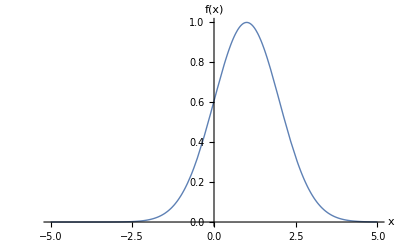

```mathematica
(*定义高斯函数*)gaussianFunction[x_]:=a*Exp[-(x-μ)^2/(2*σ^2)]

(*设置参数值*)
a=1;
μ=1;
σ=1;

(*绘制高斯函数图形*)
Plot[gaussianFunction[t],{t,-5,5},AxesLabel->{"x","f(x)"},PlotStyle->Thick]
```

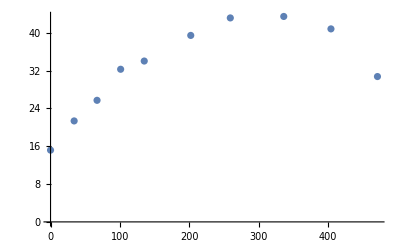

```mathematica
data1992={0,34,67,101,135,202,259,336,404,471,15.18,21.36,25.72,32.29,34.03,39.45,43.15,43.46,40.83,30.75,0,24,49,73,98,147,196,245,294,342,33.46,32.47,36.06,37.96,41.04,40.09,41.26,42.17,40.36,42.73,0,47,93,140,186,279,372,465,558,651,18.98,27.35,34.86,38.52,38.44,37.73,38.43,43.87,42.77,46.22};
len=Length[data1992]/6;
dataN=Table[data1992[[{i,i+10}]],{i,1,10}];
dataP=Table[data1992[[{i,i+10}]],{i,21,30}];
dataK=Table[data1992[[{i,i+10}]],{i,41,50}];
GN=ListPlot[dataN]
```

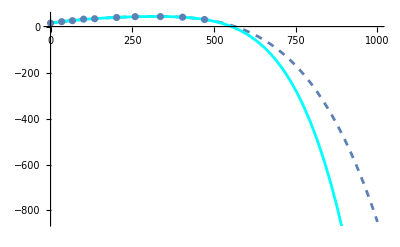

```mathematica
exp01=Fit[dataN,{1,x,x^2,x^3,x^4},{x}];
GN1=Plot[exp01,{x,0,1000},PlotStyle->Dashed];
NN=5;
exp02[NN]=Fit[dataN,Table[x^i,{i,0,NN}],x];
G02h[NN]=Plot[exp02[NN],{x,0,1000},PlotStyle->Hue[0.1 NN]];
Show[GN1,G02h[NN],GN]
```

## 关于N做拟合

44.61 ⅇ^(-0.000011 (-293.9+x)^2)

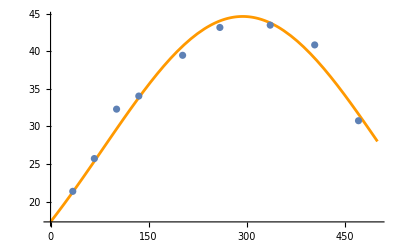

```mathematica
slu=FindFit[dataN,aa*Exp[-(t-uu)^2/(2*cc^2)],{aa,uu,cc},{t},PrecisionGoal->20,WorkingPrecision->4];
(*在FindFit函数中添加PrecisionGoal和WorkingPrecision选项，以使用更高的精度进行拟合计算。这可以减少机器精度溢出的可能性。*)
exp03=(aa*Exp[-(x-uu)^2/(2*cc^2)])/.slu
G03=Plot[exp03,{x,0,500},PlotStyle->Hue[0.1]];Show[{G03,GN}]
```

```mathematica
ObservedValue=Transpose[dataN][[2]];
PredictedValue=Table[exp03/.{x->dataN[[i,1]]},{i,1,len}];
Correlation[ObservedValue,PredictedValue]
```

0.989266

## 关于P做拟合

{aa→42.4,bb→257.6,dd→495.6}

42.4/(1+4.07×10^-6 (-257.6+x)^2)

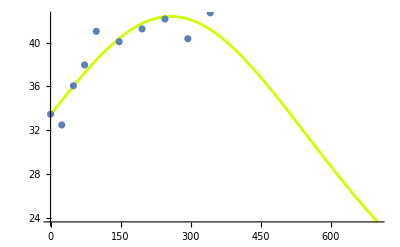

0.919604

```mathematica
GP=ListPlot[dataP];
slu=FindFit[dataP,aa/(1+((x-bb)/dd)^2),{aa,bb,dd},{x},PrecisionGoal->20,WorkingPrecision->4]
(*在FindFit函数中添加PrecisionGoal和WorkingPrecision选项，以使用更高的精度进行拟合计算。这可以减少机器精度溢出的可能性。*)
exp04=(aa/(1+((x-bb)/dd)^2))/.slu
G04=Plot[exp04,{x,0,700},PlotStyle->Hue[0.2]];
Show[{G04,GP}]
ObservedValue=Transpose[dataP][[2]];
PredictedValue=Table[exp04/.{x->dataP[[i,1]]},{i,1,len}];
Correlation[ObservedValue,PredictedValue]
```

## 对K做拟合

44.62 ⅇ^(-1.82×10^-6 (-544.7+x)^2)

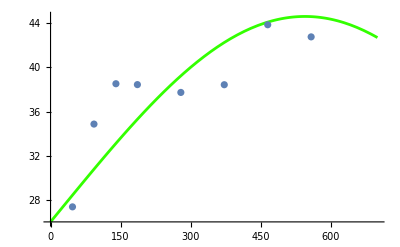

```mathematica
(*
i=5;
exp05=Fit[dataK,Table[x^k,{k,0,i}],x];
G05=Plot[exp05,{x,0,700},PlotStyle->Hue[0.15 i]];
Show[{GK,G05}]
*)
GK=ListPlot[dataK];
slu=FindFit[dataK,aa*Exp[-(t-uu)^2/(2*cc^2)],{aa,uu,cc},{t},PrecisionGoal->20,WorkingPrecision->4];
(*在FindFit函数中添加PrecisionGoal和WorkingPrecision选项，以使用更高的精度进行拟合计算。这可以减少机器精度溢出的可能性。*)
exp05=(aa*Exp[-(x-uu)^2/(2*cc^2)])/.slu
G05=Plot[exp05,{x,0,700},PlotStyle->Hue[0.3]];
Show[{G05,GK}]
```

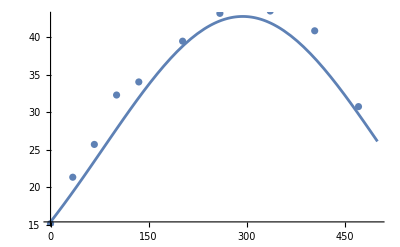

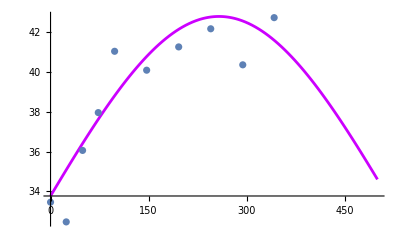

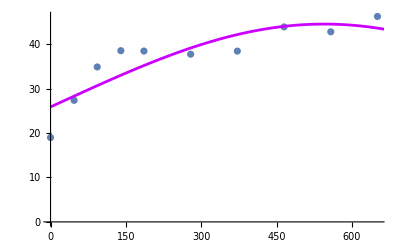

```mathematica
ObjectiveFunction[xN_,xP_,xK_]:=Module[{},((exp03/.x->xN)+(exp04/.x->xP)+(exp05/.x->xK))-2/3(dataN[[7,2]]+dataP[[7,2]]+6+dataK[[7,2]])];
GGN1=Plot[ObjectiveFunction[u,dataP[[7,1]],dataK[[7,1]]],{u,0,500}];
Show[{GGN1,GN}]
GGN2=Plot[ObjectiveFunction[dataN[[7,1]],u,dataK[[7,1]]],{u,0,500},PlotStyle->Hue[0.8],PlotRange->All,PlotPoints->100,MaxRecursion->5];
Show[{GGN2,GP}]
GGN3=Plot[ObjectiveFunction[dataN[[7,1]],dataP[[7,1]],u],{u,0,700},PlotStyle->Hue[0.8],PlotPoints->100,MaxRecursion->5];
Show[{GK,GGN3}]
```

```mathematica
FindMaximum[ObjectiveFunction[x,y,z],{{x,200,0,500},{y,200,0,350},{z,300,0,750}},PrecisionGoal->20,WorkingPrecision->5]
```

{45.743,{x→293.92,y→257.61,z→544.73}}